5/2 t Sin[t]

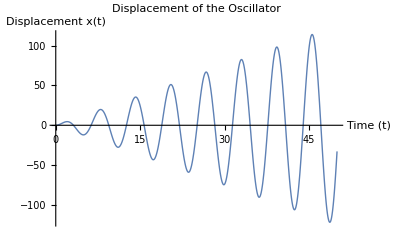

```mathematica
(*Parameters*)
m=1; (*Mass*)
k=1; (*Spring constant*)
ω0=Sqrt[k/m]; (*Natural frequency*)
F0=5; (*Amplitude of the external force*)
ω=ω0; (*Driving frequency equal to natural frequency ---this is the resonance condition*)
eqn=m x''[t]+k x[t]==F0 Cos[ω t]; (*equation of motion*)
sol=DSolve[{eqn,x[0]==0,x'[0]==0},x[t],t]; (* solve the equation of motion*)
xSolution=x[t]/. sol[[1]]//Simplify 
Plot[Evaluate[xSolution],{t,0,50},PlotRange->All,PlotLabel->"Displacement of the Oscillator",AxesLabel->{"Time (t)","Displacement x(t)"},PlotStyle->Thick]
```

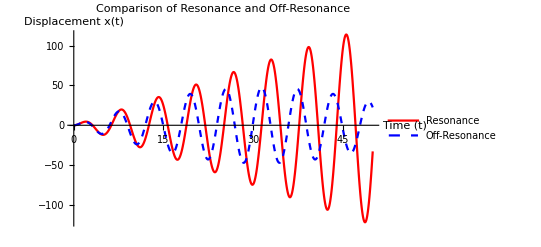

```mathematica
ωOffResonance=ω0*1.1; (*Slightly off resonance---when the driving frequency is not equal to the natural frequency*)

eqnOff=m x''[t]+k x[t]==F0 Cos[ωOffResonance t];(*equation of motion*)

solOff=DSolve[{eqnOff,x[0]==0,x'[0]==0},x[t],t];(* solve the equation of motion*)

xSolutionOff=x[t]/. solOff[[1]]//Simplify;

Plot[{Evaluate[xSolution],Evaluate[xSolutionOff]},{t,0,50},PlotRange->All,PlotLegends->{"Resonance","Off-Resonance"},PlotLabel->"Comparison of Resonance and Off-Resonance",AxesLabel->{"Time (t)","Displacement x(t)"},PlotStyle->{{Red}, {Blue,Thick,Dashed}}]
```